# Bitcoin Energy Estimates (DRAFT)

## Estimating the energy use of the Bitcoin network using two different approaches.

by Steven Black
Project home: https://github.com/StevenBlack/bitcoin-energy-estimates
Updated: October 22 2023

## Introduction

Bitcoin mining uses a Proof-of-Work consensus mechanism. This is controversial for some because that supposedly requires a lot of electrical energy. We see claims the bitcoin network “uses as much electricity as a small country”, or “requires as much electricity as Belgium, or Chile.”

This Mathematica notebook assessed those notions using the following approaches:

Presuming Bitcoin mining is marginally profitable, how much electical energy can be funded that balances actual mining rewards over time?

Given the reported hashrate, how much energy would be required to achieve that?

This paper uses Canadian dollars, partly because that’s my fiat currency, and because Canada publishes particularly good statistics about electricity generation and costs.

### Bitcoin price, block rewards, and fees

Here we outline the major factors that play in the economics of Bitcoin mining.

#### The bitcoin price right now

What is the current price of Bitcoin in Canadian dollars?

```mathematica
Now
```

Sun 22 Oct 2023 15:18:32GMT-4

```mathematica
BTCPrice =CurrencyConvert[Quantity[1,"Bitcoin"],Quantity[1,"CanadianDollars"]]
```

40 902.16 C$

#### Bitcoin block rewards

Bitcoin miners are compensated with the block reward from blocks they successfully mine, plus all the transaction fees in that block. In the current epoch (2020 - 2024) the block reward is 6 1/4 BTC.

```mathematica
blockReward = Quantity[6.25,"BTC"]
```

6.25 ฿

#### Bitcoin transaction fees per block

ASSUMPTION: the average of transaction fees per block is 0.15 BTC.

```mathematica
blockTransactionFees=Quantity[0.15,"BTC"]
```

0.15 ฿

Therefore, the total Bitcoin paid to miners for an average block, denominated in Bitcoin.

```mathematica
blockRewardPlusFees=(blockReward+blockTransactionFees)
```

6.4 ฿

#### The actual block rate

Historically Bitcoin blocks land at a rate faster then the block time target (6 per hour, or 144 blocks per day).  Let's recon an average block rate over a sample interval to present day:

```mathematica
blockchainSampleInterval = 100000;
sampleIntervalTime =Now - BlockchainBlockData[-blockchainSampleInterval]["Timestamp"]
```

682.276 days

```mathematica
blockTime=UnitConvert[sampleIntervalTime/blockchainSampleInterval,MixedUnit[{"Minutes","Seconds"}]]
```

9 49.4863

```mathematica
blockRate = Quantity[Quantity[1,"Hours"]/blockTime,"per Hour"]
```

6.10701 per hour

#### Total miner compensation, per hour

```mathematica
blockRewardPlusFeesPerHour=blockRewardPlusFees*blockRate
```

39.0849 ฿

#### Bitcoin price in Canadian dollars as a time series

Let's gather data on bitcoin price over the past sampleIntervalTime.

```mathematica
btcPriceOverTime=CurrencyConvert["Bitcoin","CanadianDollars",{Now - sampleIntervalTime,Now}];
```

Let's graph that bitcoin price over time.

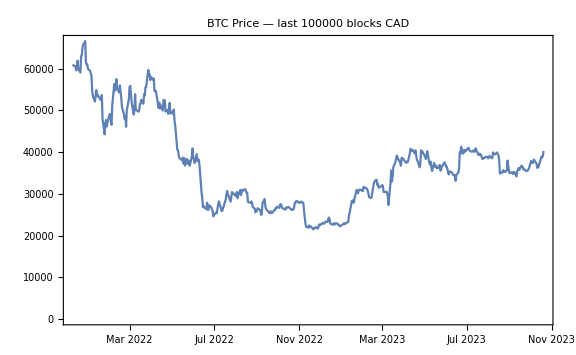

```mathematica
DateListPlot[
btcPriceOverTime,
PlotLabel->"BTC Price" <> "  — " <> "last " <> ToString[blockchainSampleInterval]<> " blocks\nCAD"
,FrameTicks->{Automatic,All}
,GridLines-> Automatic
,ImageSize->Large
]
```

#### Average bitcoin price over our sample time

```mathematica
btcPriceAvg=Mean[btcPriceOverTime]
```

36 978.33 C$

## 1. Assuming mining is ecomomically marginal, how much electricity could be funded by mining rewards?

### Global revenue per hour

The value, in Canadian Dollars, of all Bitcoin mined globally, per hour.

```mathematica
blockCADperHour=Quantity[QuantityMagnitude[blockRewardPlusFeesPerHour], "per Hour"]* btcPriceAvg
```

1.44529×10^6 C$

### Electricity cost, per kWh

See: https://www.hydroquebec.com/business/customer-space/rates/comparison-electricity-prices.html

-Graphics-

Let’s presume that nobody in their right mind would want to mine Bitcoin in New York or Boston. Here's the distribution of electricity input costs from the other 5 locations.

```mathematica
electricityInputCost = Quantity[
Around[
{0.0969,0.1042,0.1169,0.1365,0.1438}
]
,"CanadianDollars"
] /Quantity[1, "kWh"]
```

(0.1200.020) C$

### Business cost assumption

Let’s presume 85% of mining revenue is available to pay electricity cost. The rest covers wages, maintenance, depreciation, and taxes.

```mathematica
availableForElectricity = 0.85
```

0.85

### Energy economically sustainable

```mathematica
btcPower=(blockCADperHour*availableForElectricity)/electricityInputCost
```

1.030.1710^7 kW

Cognitively we can say, Bitcoin's power consumption is in the order of 10 GWH.

```mathematica
AnnualEnergyConsumption = UnitConvert[
btcPower* Quantity[365*24,"Hours"] 
,"TWh"
]
```

(90.15.) h TW

Cognitively we can say, Bitcoin's annual energy consumption is in the order of 90 TWH.

### Comparisons with large power generation facilities or regions

Let’s compare the Bitcoin network with the power and energy that generated, or used, by various things.

Here's the raw data for various generation facilities and regions.

```mathematica
generators = {
<|"name" -> "Robert-Bourassa generating station", "capacity"->Quantity[5616, "Megawatts"]|>
,<|"name" -> "Grand Coolee Dam (USA)", "capacity"->Quantity[6809, "Megawatts"]|>
,<|"name" -> "Three Gorges Dam (China)", "capacity"->Quantity[22500, "Megawatts"]|>
,<|"name" -> "Province of Québec (2019)", "capacity"->Quantity[212.9, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
};
```

```mathematica
Table[{#name,btcPower/#capacity}&[generators[[x]]],{x,1,4}]//Grid//Framed
```

Robert-Bourassa generating station | (1.830.31) 
Grand Coolee Dam (USA) | (1.510.25) 
Three Gorges Dam (China) | (0.460.08) 
Province of Québec (2019) | (0.420.07)

## 2. Given the reported hashrate, how much energy would be required to achieve that?

Coming soon.

## Appendix

### Robert-Bourassa generating station — a.k.a. “LG-2”

Here we compare the power consumption of the bitcoin network with the power generation capacity of the Robert Bourassa generating station in the James Bay region of northern Québec. 
See https://en.wikipedia.org/wiki/Robert-Bourassa_generating_station

```mathematica
RobertBourassaDam = Quantity[5616, "Megawatts"]//UnitSimplify//N
```

5.616 GW

What is Bitcoin’s global energy use in terms of LG-2?

```mathematica
btcPower/RobertBourassaDam
```

(1.830.31)

### Province of Québec

In 2019 the Province of Québec produced 212.9 TWh of electricity.

What is Bitcoin’s global energy use as a proportion of Québec’s electricity production in 2019?

```mathematica
Québec2019=Quantity[212.9, "Hours" "Terawatts"]
```

212.9 h TW

```mathematica
Québec2019day=Québec2019/Quantity[365, "Days"]//UnitSimplify
```

24.3037 GW

```mathematica
btcPower /Québec2019day
```

(0.420.07)

### Province of Ontario

See https://www.cer-rec.gc.ca/en/data-analysis/energy-markets/provincial-territorial-energy-profiles/provincial-territorial-energy-profiles-ontario.html

In 2019, the average annual power consumption per capita in Ontario was 9.6 megawatt-hours (MWh).

```mathematica
Ontario2019PerCapita = Quantity[9.6,"Hours"*"Megawatts"/"People"]/Quantity[24*365,"Hours"];
Ontario2019PerCapita = UnitConvert[Ontario2019PerCapita,Quantity[, "Kilowatts"]/Quantity[, "People"]]
```

1.09589 kW/person

```mathematica
(btcPower/Ontario2019PerCapita)
```

9.41.610^6 people

### United States

See https://www.worlddata.info/america/usa/energy-consumption.php

```mathematica
USAPerCapita = Quantity[11.757,"Hours"*"Megawatts"/"People"]/Quantity[24*365,"Hours"];
USAPerCapita = UnitConvert[USAPerCapita,Quantity[, "Kilowatts"]/Quantity[, "People"]]
```

1.34212 kW/person

```mathematica
(btcPower/USAPerCapita)
```

7.61.310^6 people

### Europe

Again see See https://www.worlddata.info/america/usa/energy-consumption.php

```mathematica
EuropePerCapita = Quantity[5.462,"Hours"*"Megawatts"/"People"]/Quantity[24*365,"Hours"];
EuropePerCapita = UnitConvert[EuropePerCapita,Quantity[, "Kilowatts"]/Quantity[, "People"]]
```

0.623516 kW/person

```mathematica
(btcPower/EuropePerCapita)
```

1.650.2810^7 people